```mathematica
nries=NDSolve[{y''[t]-Cos[t]*y'[t]-(Sin[t]+1)*y[t]==-3+Sin[t]-2,y[0]==1,y[Pi]==1},y,t]
```

{{y→InterpolatingFunction[{{0., 3.14159}}, <>]}}

```mathematica
yrn[t_]=y[t]/.nries[[1]]
```

InterpolatingFunction[{{0., 3.14159}}, <>][t]

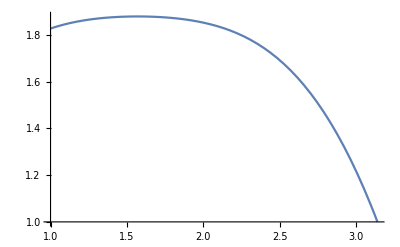

```mathematica
Plot[yrn[t],{t,1,Pi}]
```